```mathematica
data=
Import["/Users/epersico/Google Drive/GitHub/Map Files/Good Data/20170518/run2/widths/a_0.640000_m_3_n_5_widths.out","Table"]
```

{{0.01,0.00048},{0.02,0.00048},{0.03,0.00048},{0.04,0.00048},{0.05,0.00048},{0.06,0.00072},{0.07,0.00096},{0.08,0.0012},{0.09,0.00168},{0.1,0.00216},{0.11,0.00288},{0.12,0.0036},{0.13,0.00432},{0.14,0.00528},{0.15,0.00612},{0.16,0.0072},{0.17,0.00816},{0.18,0.00936},{0.19,0.01056},{0.2,0.01188},{0.21,0.01332},{0.22,0.01476},{0.23,0.0162},{0.24,0.01776},{0.25,0.01932},{0.26,0.021},{0.27,0.0228},{0.28,0.0246},{0.29,0.0264},{0.3,0.0282},{0.31,0.03012},{0.32,0.03216},{0.33,0.03408},{0.34,0.036},{0.35,0.03816},{0.36,0.0402},{0.37,0.04224},{0.38,0.04428},{0.39,0.04644},{0.4,0.04848},{0.41,0.05052},{0.42,0.05232},{0.43,0.054},{0.44,0.057},{0.45,0.05892},{0.46,0.06192},{0.47,0.06468},{0.48,0.06732},{0.49,0.0702},{0.5,0.075},{0.51,0.07608},{0.52,0.0774},{0.53,0.08268},{0.54,0.08856},{0.55,0.08424},{0.56,0.09228},{0.57,0.1008},{0.58,0.10428},{0.59,0.10152},{0.6,0.09792},{0.61,0.09168},{0.62,0.04644}}

```mathematica
Length[data]
```

62

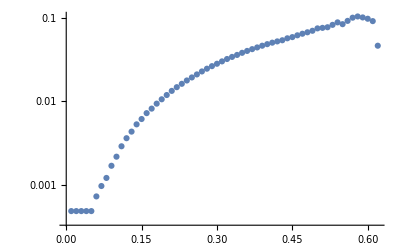

```mathematica
ListLogPlot[data]
```

FittedModel[-0.000913092+0.271813 x^1.87026]

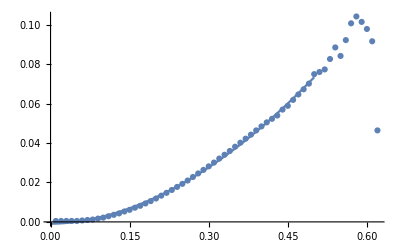

```mathematica
nlm=NonlinearModelFit[data[[1;;50,All]],a +b x^c,{a,b,c},x]
Show[ListPlot[data],Plot[nlm[x],{x,0,0.5}]]
```

```mathematica
logdata = data;
logdata[[All,2]] = Log[logdata[[All,2]]];
```

```mathematica
line1 = Fit[logdata[[100;;200,All]],{1,x},x]
```

Part::take: Cannot take positions 100 through 200 in {{0.01,-7.64172},{0.02,-7.64172},{0.03,-7.64172},{0.04,-7.64172},{0.05,-7.64172},{0.06,-7.23626},{0.07,-6.94858},{0.08,-6.72543},«35»,{0.44,-2.8647},{0.45,-2.83157},{0.46,-2.78191},{0.47,-2.7383},{0.48,-2.6983},{0.49,-2.65641},{0.5,-2.59027},«12»}.

Fit::fitd: First argument {{0.01,-7.64172},{0.02,-7.64172},{0.03,-7.64172},{0.04,-7.64172},{0.05,-7.64172},{0.06,-7.23626},{0.07,-6.94858},{0.08,-6.72543},«35»,{0.44,-2.8647},{0.45,-2.83157},{0.46,-2.78191},{0.47,-2.7383},{0.48,-2.6983},{0.49,-2.65641},{0.5,-2.59027},«12»}⟦«1»⟧ in Fit is not a list or a rectangular array.

Fit[{{0.01,-7.64172},{0.02,-7.64172},{0.03,-7.64172},{0.04,-7.64172},{0.05,-7.64172},{0.06,-7.23626},{0.07,-6.94858},{0.08,-6.72543},{0.09,-6.38896},{0.1,-6.13765},{0.11,-5.84996},{0.12,-5.62682},{0.13,-5.4445},{0.14,-5.24383},{0.15,-5.09619},{0.16,-4.93367},{0.17,-4.80851},{0.18,-4.67131},{0.19,-4.55068},{0.2,-4.4329},{0.21,-4.31849},{0.22,-4.21583},{0.23,-4.12274},{0.24,-4.03081},{0.25,-3.94661},{0.26,-3.86323},{0.27,-3.78099},{0.28,-3.70501},{0.29,-3.63439},{0.3,-3.56843},{0.31,-3.50257},{0.32,-3.43703},{0.33,-3.37904},{0.34,-3.32424},{0.35,-3.26597},{0.36,-3.21389},{0.37,-3.16439},{0.38,-3.11722},{0.39,-3.06959},{0.4,-3.0266},{0.41,-2.98539},{0.42,-2.95038},{0.43,-2.91877},{0.44,-2.8647},{0.45,-2.83157},{0.46,-2.78191},{0.47,-2.7383},{0.48,-2.6983},{0.49,-2.65641},{0.5,-2.59027},{0.51,-2.57597},{0.52,-2.55877},{0.53,-2.49278},{0.54,-2.42407},{0.55,-2.47409},{0.56,-2.38293},{0.57,-2.29462},{0.58,-2.26068},{0.59,-2.2875},{0.6,-2.3236},{0.61,-2.38945},{0.62,-3.06959}}⟦100;;200,All⟧,{1,x},x]

```mathematica
Fit[logdata[[10;;100,All]],{1,x},x]
```

Part::take: Cannot take positions 10 through 100 in {{0.01,-7.64172},{0.02,-7.64172},{0.03,-7.64172},{0.04,-7.64172},{0.05,-7.64172},{0.06,-7.23626},{0.07,-6.94858},{0.08,-6.72543},«35»,{0.44,-2.8647},{0.45,-2.83157},{0.46,-2.78191},{0.47,-2.7383},{0.48,-2.6983},{0.49,-2.65641},{0.5,-2.59027},«12»}.

Fit::fitd: First argument «1» in Fit is not a list or a rectangular array.

Fit[{{0.01,-7.64172},{0.02,-7.64172},{0.03,-7.64172},{0.04,-7.64172},{0.05,-7.64172},{0.06,-7.23626},{0.07,-6.94858},{0.08,-6.72543},{0.09,-6.38896},{0.1,-6.13765},{0.11,-5.84996},{0.12,-5.62682},{0.13,-5.4445},{0.14,-5.24383},{0.15,-5.09619},{0.16,-4.93367},{0.17,-4.80851},{0.18,-4.67131},{0.19,-4.55068},{0.2,-4.4329},{0.21,-4.31849},{0.22,-4.21583},{0.23,-4.12274},{0.24,-4.03081},{0.25,-3.94661},{0.26,-3.86323},{0.27,-3.78099},{0.28,-3.70501},{0.29,-3.63439},{0.3,-3.56843},{0.31,-3.50257},{0.32,-3.43703},{0.33,-3.37904},{0.34,-3.32424},{0.35,-3.26597},{0.36,-3.21389},{0.37,-3.16439},{0.38,-3.11722},{0.39,-3.06959},{0.4,-3.0266},{0.41,-2.98539},{0.42,-2.95038},{0.43,-2.91877},{0.44,-2.8647},{0.45,-2.83157},{0.46,-2.78191},{0.47,-2.7383},{0.48,-2.6983},{0.49,-2.65641},{0.5,-2.59027},{0.51,-2.57597},{0.52,-2.55877},{0.53,-2.49278},{0.54,-2.42407},{0.55,-2.47409},{0.56,-2.38293},{0.57,-2.29462},{0.58,-2.26068},{0.59,-2.2875},{0.6,-2.3236},{0.61,-2.38945},{0.62,-3.06959}}⟦10;;100,All⟧,{1,x},x]